```mathematica
TextStructure["Jupiter is the biggest planet in our solar system, eleven times bigger in diameter than Earth and two-and-a-half times more massive than all the other planets put together. Jupiter has no solid surface. Beneath the gas clouds lies hot, liquid hydrogen, then a layer of hydrogen in a form similar to liquid metal, and finally a rocky core. Jupiter has a faint ring around its equator made of microscopic dust particles.", "DependencyGraphs"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TextStructure["Saturn's rings are made up of chunks of ice and dust whizzing around the planet at high speed. They vary in size from particles as small as sand grains to huge boulders. No one is sure where this material came from. It could be the remains of ancient moons or maybe the debris of comets that came too close. drwillway8489 ancient in the astrological sense like Icarus, because why not?", "ConstituentGraphs"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TextStructure["Temperature is a measure of how hot or cold something is. Things that have high temperature are hotter than things that have lower temperature, because they have more heat energy inside them. Any object can transfer heat energy to a colder object. As it does so, it cools down and its temperature falls. The colder object warms up and its temperature rises.", "DependencyGraphs"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
CommunityGraphPlot[Graph[Flatten[Select[{"apology"->"statement","convenience"->"comfort","praise"->"glory","praise"->"honor","praise"->"criticism","praise"->"blessing","praise"->"appreciation"},UnsameQ[#,{}]&]]],VertexLabels->"Name"]
```

-Graphics-

```mathematica
ConvertEdges[Graph_]:=Table[DirectedEdge[x[[1]],x[[2]]],{x,EdgeList[Graph]}]
```

```mathematica
ConstituentDepthFunction[Graph_]:=Module[{vertexout=DeleteCases[Table[If[Length[n]==1,n],{n,VertexInComponent[Graph,#]&/@VertexList[Graph]}],Null]//Flatten,vertexin=DeleteCases[Table[If[Length[n]==1,n],{n,VertexOutComponent[Graph,#]&/@VertexList[Graph]}],Null]//Flatten},Max[Table[Length[n],{n,FindShortestPath[Graph,vertexout[[1]],#]&/@vertexin}]]]
```

```mathematica
TextStructure["A cat sat on a mat.","ConstituentGraphs"][[1]]
```

-Graphics-

```mathematica
e={UndirectedEdge[1,2],UndirectedEdge[3,4]};
e
e/.UndirectedEdge[x_,y_]->{x,y}
```

{1<->2,3<->4}

{{1,2},{3,4}}

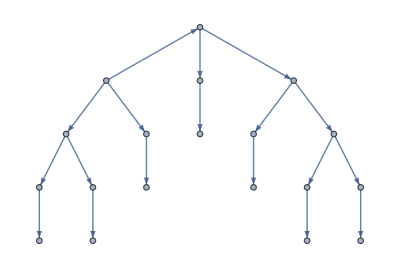

```mathematica
Graph[ConvertEdges[TextStructure["A cat sat on a mat.","ConstituentGraphs"][[1]]]]
```

```mathematica
CommunityGraphPlot[Graph[Flatten[Select[{"apology"->"statement","convenience"->"comfort","praise"->"glory","praise"->"honor","praise"->"criticism","praise"->"blessing","praise"->"appreciation"},UnsameQ[#,{}]&]]],VertexLabels->"Name"]
```

-Graphics-

```mathematica
text = StringSplit["Paper burns at 363°F is to Natural gas burns at 220°F as Paper burns at 457K is to Natural gas burns at 1,933K. Kelvin, being close to Celsius... is a linear conversion, the conversion constants being evident from the pages regarding Saturn and his friends. Fahrenheit, being 1,220° by the adjacent 660°C with the observation that we can multiply by 9/5 and add 32, is similarly the result of the illogical arrangement of data; for example, all that consistent logical progression gives us, for example not the deceptive aspect of consistency that is the principle of Test of Observation Skills: Posted below are 4 pages from e.encyclopedia Science 1st edition. there is an error in each of the last two photos (about Saturn and Temperature)....",{" ", ". ", ", ","
"}]
```

{Paper,burns,at,363°F,is,to,Natural,gas,burns,at,220°F,as,Paper,burns,at,457K,is,to,Natural,gas,burns,at,1,933K,Kelvin,being,close,to,Celsius..,is,a,linear,conversion,the,conversion,constants,being,evident,from,the,pages,regarding,Saturn,and,his,friends,Fahrenheit,being,1,220°,by,the,adjacent,660°C,with,the,observation,that,we,can,multiply,by,9/5,and,add,32,is,similarly,the,result,of,the,illogical,arrangement,of,data;,for,example,all,that,consistent,logical,progression,gives,us,for,example,not,the,deceptive,aspect,of,consistency,that,is,the,principle,of,Test,of,Observation,Skills:,Posted,below,are,4,pages,from,e.encyclopedia,Science,1st,edition,there,is,an,error,in,each,of,the,last,two,photos,(about,Saturn,and,Temperature)....}

```mathematica
Thread[Rule[Drop[text,-1],Drop[text,1]]]
```

{Paper→burns,burns→at,at→363°F,363°F→is,is→to,to→Natural,Natural→gas,gas→burns,burns→at,at→220°F,220°F→as,as→Paper,Paper→burns,burns→at,at→457K,457K→is,is→to,to→Natural,Natural→gas,gas→burns,burns→at,at→1,933K,1,933K→Kelvin,Kelvin→being,being→close,close→to,to→Celsius..,Celsius..→is,is→a,a→linear,linear→conversion,conversion→the,the→conversion,conversion→constants,constants→being,being→evident,evident→from,from→the,the→pages,pages→regarding,regarding→Saturn,Saturn→and,and→his,his→friends,friends→Fahrenheit,Fahrenheit→being,being→1,220°,1,220°→by,by→the,the→adjacent,adjacent→660°C,660°C→with,with→the,the→observation,observation→that,that→we,we→can,can→multiply,multiply→by,by→9/5,9/5→and,and→add,add→32,32→is,is→similarly,similarly→the,the→result,result→of,of→the,the→illogical,illogical→arrangement,arrangement→of,of→data;,data;→for,for→example,example→all,all→that,that→consistent,consistent→logical,logical→progression,progression→gives,gives→us,us→for,for→example,example→not,not→the,the→deceptive,deceptive→aspect,aspect→of,of→consistency,consistency→that,that→is,is→the,the→principle,principle→of,of→Test,Test→of,of→Observation,Observation→Skills:,Skills:→Posted,Posted→below,below→are,are→4,4→pages,pages→from,from→e.encyclopedia,e.encyclopedia→Science,Science→1st,1st→edition,edition→there,there→is,is→an,an→error,error→in,in→each,each→of,of→the,the→last,last→two,two→photos,photos→(about,(about→Saturn,Saturn→and,and→Temperature)....}

```mathematica
Drop[text,-1]
```

{Paper,burns,at,363°F,is,to,Natural,gas,burns,at,220°F,as,Paper,burns,at,457K,is,to,Natural,gas,burns,at,1,933K,Kelvin,being,close,to,Celsius..,is,a,linear,conversion,the,conversion,constants,being,evident,from,the,pages,regarding,Saturn,and,his,friends,Fahrenheit,being,1,220°,by,the,adjacent,660°C,with,the,observation,that,we,can,multiply,by,9/5,and,add,32,is,similarly,the,result,of,the,illogical,arrangement,of,data;,for,example,all,that,consistent,logical,progression,gives,us,for,example,not,the,deceptive,aspect,of,consistency,that,is,the,principle,of,Test,of,Observation,Skills:,Posted,below,are,4,pages,from,e.encyclopedia,Science,1st,edition,there,is,an,error,in,each,of,the,last,two,photos,(about,Saturn,and}

```mathematica
Range[10-1]
```

{1,2,3,4,5,6,7,8,9}

```mathematica
(n|->n->n+1)/@{"hello","everyone","there"}
```

{hello→1+hello,everyone→1+everyone,there→1+there}

```mathematica
Rule[Range[10-1],Range[2,10]]
```

{1,2,3,4,5,6,7,8,9}→{2,3,4,5,6,7,8,9,10}

```mathematica
CommunityGraphPlot[Graph[Flatten[Select[{"apology"->"statement","convenience"->"comfort","praise"->"glory","praise"->"honor","praise"->"criticism","praise"->"blessing","praise"->"appreciation"},UnsameQ[#,{}]&]]],VertexLabels->"Name"]
```

-Graphics-

```mathematica
@ https://community.wolfram.com/groups/-/m/t/2575414 and Mads Bahrami's string-universal (for example, not numbers like Paul Abbott's (n|->n->n+1)/@Range[n-1]) Thread[Rule[Range[n-1],Range[2,n]]].
```

```mathematica
With[{text=StringSplit["What do you call an arrow function that cares about where it is invoked & called (for example, not about where it is defined)? The idea is that the 8 year old has a lot to look forward to, therefore is most analogous to the arrow function; he's taking his true calling and following the laws of physics, rather than being affected by the laws of physics. He thus finds the illogical arrangement in the data, caring about the logical progression of the data (for example, not its definition).",{" ", ". ", ", ","
"}]},
CommunityGraphPlot[Graph[Flatten[Select[Thread[Rule[Drop[text,-1],Drop[text,1]]],UnsameQ[#,{}]&]]],VertexLabels->"Name"]]
```

-Graphics-

```mathematica
data={{1,3,2,1,3,1,3,1,2,1,2},{1,2,1,2,1,2,3,2,3,2,3},{1,3,2,1,2,3,1,2,1,3,2},{1,3,2,1,2,1,2,1,3,1,3},{1,2,3,1,3,1,3,2,1,2,1}};
Partition[#,2,1]&/@data
DirectedEdge@@@Partition[#,2,1]&/@data
```

{{{1,3},{3,2},{2,1},{1,3},{3,1},{1,3},{3,1},{1,2},{2,1},{1,2}},{{1,2},{2,1},{1,2},{2,1},{1,2},{2,3},{3,2},{2,3},{3,2},{2,3}},{{1,3},{3,2},{2,1},{1,2},{2,3},{3,1},{1,2},{2,1},{1,3},{3,2}},{{1,3},{3,2},{2,1},{1,2},{2,1},{1,2},{2,1},{1,3},{3,1},{1,3}},{{1,2},{2,3},{3,1},{1,3},{3,1},{1,3},{3,2},{2,1},{1,2},{2,1}}}

{{1->3,3->2,2->1,1->3,3->1,1->3,3->1,1->2,2->1,1->2},{1->2,2->1,1->2,2->1,1->2,2->3,3->2,2->3,3->2,2->3},{1->3,3->2,2->1,1->2,2->3,3->1,1->2,2->1,1->3,3->2},{1->3,3->2,2->1,1->2,2->1,1->2,2->1,1->3,3->1,1->3},{1->2,2->3,3->1,1->3,3->1,1->3,3->2,2->1,1->2,2->1}}

```mathematica
ConvertEdges[g]
```

Table::iterb: Iterator {x,EdgeList[g]} does not have appropriate bounds.

Table[x⟦1⟧->x⟦2⟧,{x,EdgeList[g]}]

```mathematica
CommunityGraphPlot[Graph[Flatten[Select[g,UnsameQ[#,{}]&]]],VertexLabels->"Name"]
```

Select::normal: Nonatomic expression expected at position 1 in Select[g,#1=!={}&].

CommunityGraphPlot::graph: A graph object is expected at position 1 in CommunityGraphPlot[Graph[Select[g,#1=!={}&]],VertexLabels→Name].

CommunityGraphPlot[Graph[Select[g,#1=!={}&]],VertexLabels→Name]

```mathematica
ConstituentDepthFunction[Graph[ConvertEdges[TextStructure["A cat sat on a mat.","ConstituentGraphs"][[1]]]]]
```

6

```mathematica
With[{text=StringSplit["What do you call an arrow function that cares about where it is invoked & called (for example, not about where it is defined)? The idea is that the 8 year old has a lot to look forward to, therefore is most analogous to the arrow function; he's taking his true calling and following the laws of physics, rather than being affected by the laws of physics. He thus finds the illogical arrangement in the data, caring about the logical progression of the data (for example, not its definition).",{" ",". ",", ","
"}]},CommunityGraphPlot[Graph[Flatten[Select[Thread[Rule[Drop[text,-1],Drop[text,1]]],UnsameQ[#,{}]&]]],VertexLabels->"Name"]]
```

-Graphics-

```mathematica
With[{text=StringSplit["What do you call an arrow function that cares about where it is invoked & called (for example, not about where it is defined)? The idea is that the 8 year old has a lot to look forward to, therefore is most analogous to the arrow function; he's taking his true calling and following the laws of physics, rather than being affected by the laws of physics. He thus finds the illogical arrangement in the data, caring about the logical progression of the data (for example, not its definition).",{" ",". ",", ","
"}]},CommunityGraphPlot[Graph[Flatten[Select[Thread[Rule[Drop[text,-1],Drop[text,1]]],UnsameQ[#,{}]&]]],VertexLabels->"Name"]]
```

-Graphics-

```mathematica
Style[
TextStructure["A fair maiden has been locked in a tall tower by an evil knight, but her golden hair is magical and she can grow it at will-long enough for her champion to climb up and rescue her. When she casts her spell, her hair will grow by half its initial length in the first second, then by a third of its new length in the next second, then by a quarter of its length in the following second, and so on. Now, given that her hair is one meter long to start with and the tower is fifty meters high. When or if her hair will reach the ground?"], FontSize->12, FontColor->White, FontFamily->"Times", Bold, Background->GrayLevel[0.2]]
```

A
Determinerfair
Adjectivemaiden
Noun
Noun Phrase  has
Verb  been
Verb  locked
Verb  in
Preposition  a
Determinertall
Adjectivetower
Noun
Noun Phrase
Prepositional Phrase  by
Preposition  an
Determinerevil
Adjectiveknight
Noun
Noun Phrase
Prepositional Phrase
Verb Phrase
Verb Phrase
Verb Phrase
Clause,
Punctuationbut
Conjunction    her
Pronoungolden
Adjectivehair
Noun
Noun Phrase  is
Verb  magical
Adjective
Adjective Phrase
Verb Phraseand
Conjunction  she
Pronoun
Noun Phrase  can
Verb  grow
Verb  it
Pronoun
Noun Phrase  at
Preposition  will-long
Adjectiveenough
Adverb  for
Preposition  her
Pronounchampion
Noun
Noun Phrase
Prepositional Phrase    to
Preposition    climb
Verb  up
Particle
Particle
Verb Phraseand
Conjunction  rescue
Verb  her
Pronoun
Noun Phrase
Verb Phrase
Verb Phrase
Verb Phrase
Clause
Adjective Phrase
Prepositional Phrase
Verb Phrase
Verb Phrase
Clause.
Punctuation
Sentence |       When
Wh-Adverb
Wh-Adverb Phrase  she
Pronoun
Noun Phrase  casts
Verb  her
Pronounspell
Noun
Noun Phrase
Verb Phrase
Clause,
Punctuation  her
Pronounhair
Noun
Noun Phrase  will
Verb  grow
Verb  by
Preposition  half
Determinerits
Pronouninitial
Adjectivelength
Noun
Noun Phrase
Prepositional Phrase  in
Preposition    the
Determinerfirst
Adjectivesecond
Noun
Noun Phrase,
Punctuation      then
Adverb
Adverb Phrase  by
Preposition    a
Determinerthird
Adjective
Noun Phrase  of
Preposition    its
Pronounnew
Adjectivelength
Noun
Noun Phrase  in
Preposition  the
Determinernext
Adjectivesecond
Noun
Noun Phrase
Prepositional Phrase
Noun Phrase
Prepositional Phrase
Noun Phrase
Prepositional Phrase,
Punctuation  then
Adverb
Adverb Phrase  by
Preposition    a
Determinerquarter
Noun
Noun Phrase  of
Preposition    its
Pronounlength
Noun
Noun Phrase  in
Preposition  the
Determinerfollowing
Verbsecond
Noun
Noun Phrase
Prepositional Phrase
Noun Phrase
Prepositional Phrase
Noun Phrase
Prepositional Phrase
Prepositional Phrase,
Punctuationand
Conjunction  so
Preposition    on
Preposition
Prepositional Phrase
Fragment
Clause
Unlike Coordinated Phrase
Noun Phrase
Prepositional Phrase
Verb Phrase
Verb Phrase.
Punctuation
Sentence |     Now
Adverb
Adverb Phrase,
Punctuation  given
Verb  that
Preposition  her
Pronounhair
Noun
Noun Phrase  is
Verb    one
Numeralmeter
Noun
Noun Phraselong
Adjective
Adjective Phrase    to
Preposition  start
Verb  with
Preposition
Prepositional Phrase
Verb Phrase
Verb Phrase
Clause
Verb Phraseand
Conjunction  the
Determinertower
Noun
Noun Phrase  is
Verb  fifty
Adverbmeters
Adverbhigh
Adjective
Adjective Phrase
Verb Phrase
Clause
Verb Phrase.
Punctuation
Sentence |         When
Wh-Adverb
Wh-Adverb Phraseor
Conjunctionif
Preposition
Unlike Coordinated Phrase  her
Pronounhair
Noun
Noun Phrase  will
Verb  reach
Verb  the
Determinerground
Noun
Noun Phrase
Verb Phrase
Verb Phrase
Clause?
Punctuation
Sentence

```mathematica
With[{text=StringSplit["A fair maiden has been locked in a tall tower by an evil knight, but her golden hair is magical and she can grow it at will-long enough for her champion to climb up and rescue her. When she casts her spell, her hair will grow by half its initial length in the first second, then by a third of its new length in the next second, then by a quarter of its length in the following second, and so on. Now, given that her hair is one meter long to start with and the tower is fifty meters high. When or if her hair will reach the ground?",{" ",". ",", ","
"}]},CommunityGraphPlot[
Graph[Flatten[Select[Thread[Rule[Drop[text,-1],Drop[text,1]]],UnsameQ[#,{}]&]]],
VertexLabels->"Name",
AspectRatio->1,
Method->"SpringElectrical",
PlotTheme->"Scientific"
]]
```

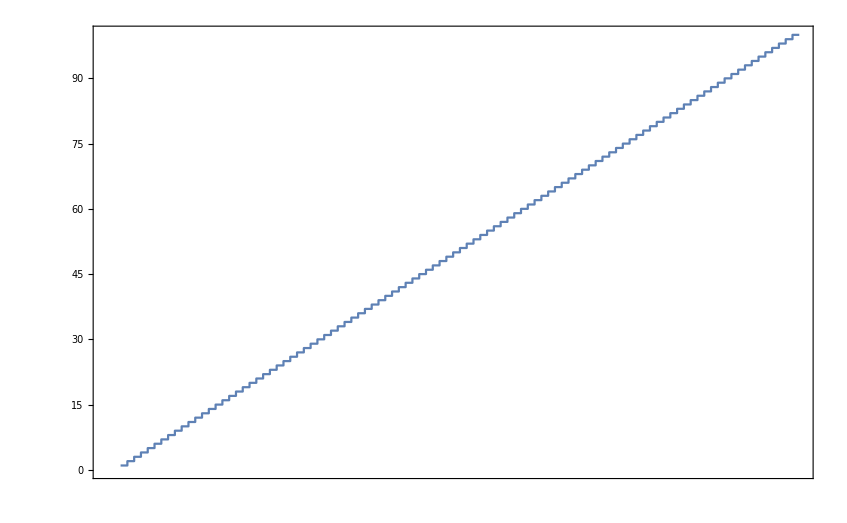

-Graphics-

```mathematica
Clear[maidenHairFn]
maidenHairFn[n_]:=maidenHairFn[n]=((n+1+1)/(n+1)) * maidenHairFn[n-1]
maidenHairFn[0]:=1

t:=maidenHairFn/@(Range[100]-1)
ts:=TimeSeries[Range[100],{t}]
DateListStepPlot[ts]
```

```mathematica
N[101/2]
```

50.5

{1/100000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000,9998,538316238022908532265945792081720692964834375370881022505036319594881303074666597890489528218131896033915413204421811103371044633040461229773379585731280899889122871961873793972905717296095915787/160000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}
 |  |  |  |

General::munfl: 1.×10^-200 2.97193341570781×10^-1889 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.×10^-200 2.97193341570781×10^-1889 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.×10^-200 2.97193341570781×10^-1889 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

ListPolarPlot::prng: Value of option PlotRange -> {{0.,3.36447648764318×10^1889},{0.,10000.}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

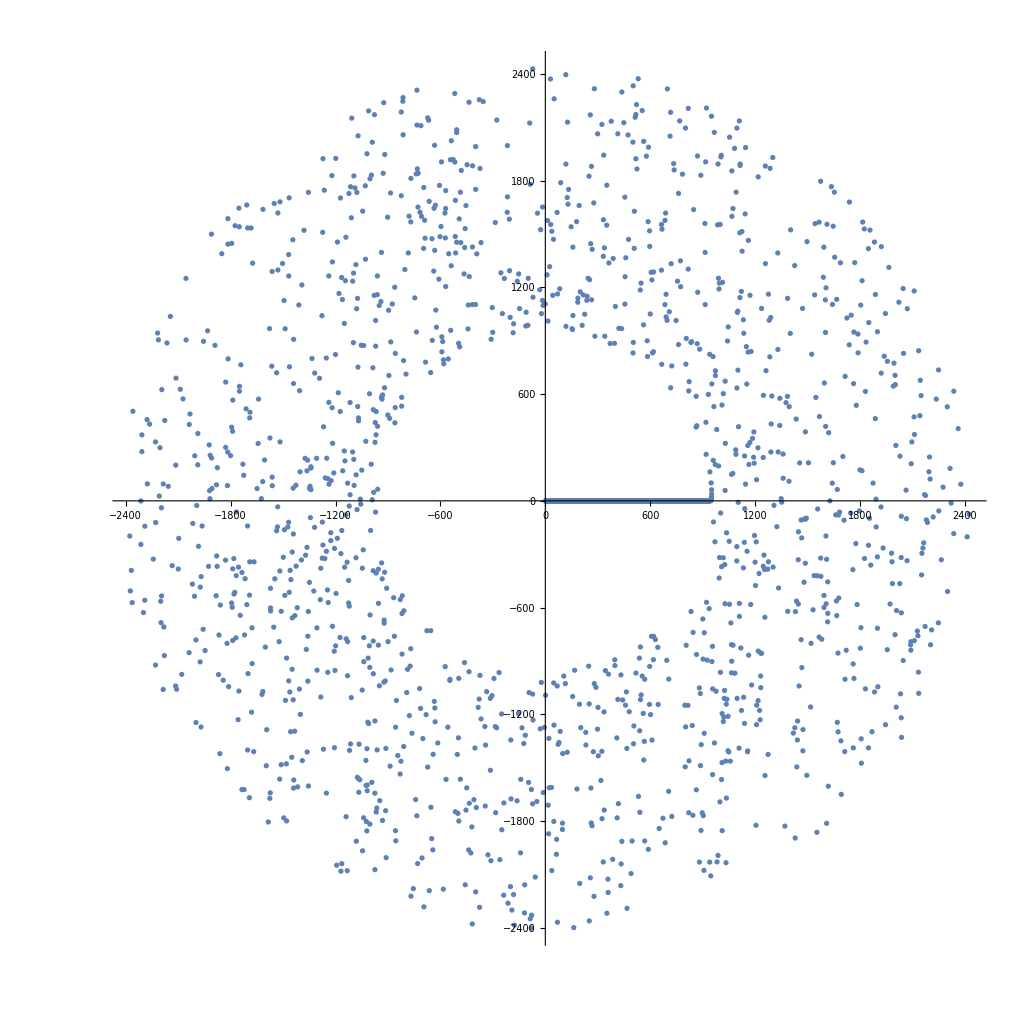

```mathematica
Clear[maidenHairFn]
(*unit:=π/250-π/500*)
maidenHairFn[n_]:=maidenHairFn[n]=maidenHairFn[n-1] + maidenHairFn[n-2]
maidenHairFn[0]:=1; maidenHairFn[1] := 1;

range:=Range[10000]
t=(maidenHairFn/@(range-1))/(10^200)

ts:=TimeSeries[range,{t}]
ListPolarPlot[ts]
```

```mathematica
N[ToPolarCoordinates[Range[10]]]
```

{19.6214,1.51981,1.46856,1.41629,1.3616,1.30221,1.23419,1.15026,1.03433,0.837981}

```mathematica
10000/(2*Pi)
```

5000/π

```mathematica
1000/(2*Pi)
```

500/π

```mathematica
Range[1000]/(1000/(2*Pi))
```

{π/500,π/250,(3 π)/500,π/125,π/100,(3 π)/250,(7 π)/500,(2 π)/125,(9 π)/500,π/50,(11 π)/500,(3 π)/125,(13 π)/500,(7 π)/250,(3 π)/100,(4 π)/125,(17 π)/500,(9 π)/250,(19 π)/500,π/25,(21 π)/500,(11 π)/250,(23 π)/500,(6 π)/125,π/20,(13 π)/250,(27 π)/500,(7 π)/125,(29 π)/500,(3 π)/50,(31 π)/500,(8 π)/125,(33 π)/500,(17 π)/250,(7 π)/100,(9 π)/125,(37 π)/500,(19 π)/250,(39 π)/500,(2 π)/25,(41 π)/500,(21 π)/250,(43 π)/500,(11 π)/125,(9 π)/100,(23 π)/250,(47 π)/500,(12 π)/125,(49 π)/500,π/10,(51 π)/500,(13 π)/125,(53 π)/500,(27 π)/250,(11 π)/100,(14 π)/125,(57 π)/500,(29 π)/250,(59 π)/500,(3 π)/25,(61 π)/500,(31 π)/250,(63 π)/500,(16 π)/125,(13 π)/100,(33 π)/250,(67 π)/500,(17 π)/125,(69 π)/500,(7 π)/50,(71 π)/500,(18 π)/125,(73 π)/500,(37 π)/250,(3 π)/20,(19 π)/125,(77 π)/500,(39 π)/250,(79 π)/500,(4 π)/25,(81 π)/500,(41 π)/250,(83 π)/500,(21 π)/125,(17 π)/100,(43 π)/250,(87 π)/500,(22 π)/125,(89 π)/500,(9 π)/50,(91 π)/500,(23 π)/125,(93 π)/500,(47 π)/250,(19 π)/100,(24 π)/125,(97 π)/500,(49 π)/250,(99 π)/500,π/5,(101 π)/500,(51 π)/250,(103 π)/500,(26 π)/125,(21 π)/100,(53 π)/250,(107 π)/500,(27 π)/125,(109 π)/500,(11 π)/50,(111 π)/500,(28 π)/125,(113 π)/500,(57 π)/250,(23 π)/100,(29 π)/125,(117 π)/500,(59 π)/250,(119 π)/500,(6 π)/25,(121 π)/500,(61 π)/250,(123 π)/500,(31 π)/125,π/4,(63 π)/250,(127 π)/500,(32 π)/125,(129 π)/500,(13 π)/50,(131 π)/500,(33 π)/125,(133 π)/500,(67 π)/250,(27 π)/100,(34 π)/125,(137 π)/500,(69 π)/250,(139 π)/500,(7 π)/25,(141 π)/500,(71 π)/250,(143 π)/500,(36 π)/125,(29 π)/100,(73 π)/250,(147 π)/500,(37 π)/125,(149 π)/500,(3 π)/10,(151 π)/500,(38 π)/125,(153 π)/500,(77 π)/250,(31 π)/100,(39 π)/125,(157 π)/500,(79 π)/250,(159 π)/500,(8 π)/25,(161 π)/500,(81 π)/250,(163 π)/500,(41 π)/125,(33 π)/100,(83 π)/250,(167 π)/500,(42 π)/125,(169 π)/500,(17 π)/50,(171 π)/500,(43 π)/125,(173 π)/500,(87 π)/250,(7 π)/20,(44 π)/125,(177 π)/500,(89 π)/250,(179 π)/500,(9 π)/25,(181 π)/500,(91 π)/250,(183 π)/500,(46 π)/125,(37 π)/100,(93 π)/250,(187 π)/500,(47 π)/125,(189 π)/500,(19 π)/50,(191 π)/500,(48 π)/125,(193 π)/500,(97 π)/250,(39 π)/100,(49 π)/125,(197 π)/500,(99 π)/250,(199 π)/500,(2 π)/5,(201 π)/500,(101 π)/250,(203 π)/500,(51 π)/125,(41 π)/100,(103 π)/250,(207 π)/500,(52 π)/125,(209 π)/500,(21 π)/50,(211 π)/500,(53 π)/125,(213 π)/500,(107 π)/250,(43 π)/100,(54 π)/125,(217 π)/500,(109 π)/250,(219 π)/500,(11 π)/25,(221 π)/500,(111 π)/250,(223 π)/500,(56 π)/125,(9 π)/20,(113 π)/250,(227 π)/500,(57 π)/125,(229 π)/500,(23 π)/50,(231 π)/500,(58 π)/125,(233 π)/500,(117 π)/250,(47 π)/100,(59 π)/125,(237 π)/500,(119 π)/250,(239 π)/500,(12 π)/25,(241 π)/500,(121 π)/250,(243 π)/500,(61 π)/125,(49 π)/100,(123 π)/250,(247 π)/500,(62 π)/125,(249 π)/500,π/2,(251 π)/500,(63 π)/125,(253 π)/500,(127 π)/250,(51 π)/100,(64 π)/125,(257 π)/500,(129 π)/250,(259 π)/500,(13 π)/25,(261 π)/500,(131 π)/250,(263 π)/500,(66 π)/125,(53 π)/100,(133 π)/250,(267 π)/500,(67 π)/125,(269 π)/500,(27 π)/50,(271 π)/500,(68 π)/125,(273 π)/500,(137 π)/250,(11 π)/20,(69 π)/125,(277 π)/500,(139 π)/250,(279 π)/500,(14 π)/25,(281 π)/500,(141 π)/250,(283 π)/500,(71 π)/125,(57 π)/100,(143 π)/250,(287 π)/500,(72 π)/125,(289 π)/500,(29 π)/50,(291 π)/500,(73 π)/125,(293 π)/500,(147 π)/250,(59 π)/100,(74 π)/125,(297 π)/500,(149 π)/250,(299 π)/500,(3 π)/5,(301 π)/500,(151 π)/250,(303 π)/500,(76 π)/125,(61 π)/100,(153 π)/250,(307 π)/500,(77 π)/125,(309 π)/500,(31 π)/50,(311 π)/500,(78 π)/125,(313 π)/500,(157 π)/250,(63 π)/100,(79 π)/125,(317 π)/500,(159 π)/250,(319 π)/500,(16 π)/25,(321 π)/500,(161 π)/250,(323 π)/500,(81 π)/125,(13 π)/20,(163 π)/250,(327 π)/500,(82 π)/125,(329 π)/500,(33 π)/50,(331 π)/500,(83 π)/125,(333 π)/500,(167 π)/250,(67 π)/100,(84 π)/125,(337 π)/500,(169 π)/250,(339 π)/500,(17 π)/25,(341 π)/500,(171 π)/250,(343 π)/500,(86 π)/125,(69 π)/100,(173 π)/250,(347 π)/500,(87 π)/125,(349 π)/500,(7 π)/10,(351 π)/500,(88 π)/125,(353 π)/500,(177 π)/250,(71 π)/100,(89 π)/125,(357 π)/500,(179 π)/250,(359 π)/500,(18 π)/25,(361 π)/500,(181 π)/250,(363 π)/500,(91 π)/125,(73 π)/100,(183 π)/250,(367 π)/500,(92 π)/125,(369 π)/500,(37 π)/50,(371 π)/500,(93 π)/125,(373 π)/500,(187 π)/250,(3 π)/4,(94 π)/125,(377 π)/500,(189 π)/250,(379 π)/500,(19 π)/25,(381 π)/500,(191 π)/250,(383 π)/500,(96 π)/125,(77 π)/100,(193 π)/250,(387 π)/500,(97 π)/125,(389 π)/500,(39 π)/50,(391 π)/500,(98 π)/125,(393 π)/500,(197 π)/250,(79 π)/100,(99 π)/125,(397 π)/500,(199 π)/250,(399 π)/500,(4 π)/5,(401 π)/500,(201 π)/250,(403 π)/500,(101 π)/125,(81 π)/100,(203 π)/250,(407 π)/500,(102 π)/125,(409 π)/500,(41 π)/50,(411 π)/500,(103 π)/125,(413 π)/500,(207 π)/250,(83 π)/100,(104 π)/125,(417 π)/500,(209 π)/250,(419 π)/500,(21 π)/25,(421 π)/500,(211 π)/250,(423 π)/500,(106 π)/125,(17 π)/20,(213 π)/250,(427 π)/500,(107 π)/125,(429 π)/500,(43 π)/50,(431 π)/500,(108 π)/125,(433 π)/500,(217 π)/250,(87 π)/100,(109 π)/125,(437 π)/500,(219 π)/250,(439 π)/500,(22 π)/25,(441 π)/500,(221 π)/250,(443 π)/500,(111 π)/125,(89 π)/100,(223 π)/250,(447 π)/500,(112 π)/125,(449 π)/500,(9 π)/10,(451 π)/500,(113 π)/125,(453 π)/500,(227 π)/250,(91 π)/100,(114 π)/125,(457 π)/500,(229 π)/250,(459 π)/500,(23 π)/25,(461 π)/500,(231 π)/250,(463 π)/500,(116 π)/125,(93 π)/100,(233 π)/250,(467 π)/500,(117 π)/125,(469 π)/500,(47 π)/50,(471 π)/500,(118 π)/125,(473 π)/500,(237 π)/250,(19 π)/20,(119 π)/125,(477 π)/500,(239 π)/250,(479 π)/500,(24 π)/25,(481 π)/500,(241 π)/250,(483 π)/500,(121 π)/125,(97 π)/100,(243 π)/250,(487 π)/500,(122 π)/125,(489 π)/500,(49 π)/50,(491 π)/500,(123 π)/125,(493 π)/500,(247 π)/250,(99 π)/100,(124 π)/125,(497 π)/500,(249 π)/250,(499 π)/500,π,(501 π)/500,(251 π)/250,(503 π)/500,(126 π)/125,(101 π)/100,(253 π)/250,(507 π)/500,(127 π)/125,(509 π)/500,(51 π)/50,(511 π)/500,(128 π)/125,(513 π)/500,(257 π)/250,(103 π)/100,(129 π)/125,(517 π)/500,(259 π)/250,(519 π)/500,(26 π)/25,(521 π)/500,(261 π)/250,(523 π)/500,(131 π)/125,(21 π)/20,(263 π)/250,(527 π)/500,(132 π)/125,(529 π)/500,(53 π)/50,(531 π)/500,(133 π)/125,(533 π)/500,(267 π)/250,(107 π)/100,(134 π)/125,(537 π)/500,(269 π)/250,(539 π)/500,(27 π)/25,(541 π)/500,(271 π)/250,(543 π)/500,(136 π)/125,(109 π)/100,(273 π)/250,(547 π)/500,(137 π)/125,(549 π)/500,(11 π)/10,(551 π)/500,(138 π)/125,(553 π)/500,(277 π)/250,(111 π)/100,(139 π)/125,(557 π)/500,(279 π)/250,(559 π)/500,(28 π)/25,(561 π)/500,(281 π)/250,(563 π)/500,(141 π)/125,(113 π)/100,(283 π)/250,(567 π)/500,(142 π)/125,(569 π)/500,(57 π)/50,(571 π)/500,(143 π)/125,(573 π)/500,(287 π)/250,(23 π)/20,(144 π)/125,(577 π)/500,(289 π)/250,(579 π)/500,(29 π)/25,(581 π)/500,(291 π)/250,(583 π)/500,(146 π)/125,(117 π)/100,(293 π)/250,(587 π)/500,(147 π)/125,(589 π)/500,(59 π)/50,(591 π)/500,(148 π)/125,(593 π)/500,(297 π)/250,(119 π)/100,(149 π)/125,(597 π)/500,(299 π)/250,(599 π)/500,(6 π)/5,(601 π)/500,(301 π)/250,(603 π)/500,(151 π)/125,(121 π)/100,(303 π)/250,(607 π)/500,(152 π)/125,(609 π)/500,(61 π)/50,(611 π)/500,(153 π)/125,(613 π)/500,(307 π)/250,(123 π)/100,(154 π)/125,(617 π)/500,(309 π)/250,(619 π)/500,(31 π)/25,(621 π)/500,(311 π)/250,(623 π)/500,(156 π)/125,(5 π)/4,(313 π)/250,(627 π)/500,(157 π)/125,(629 π)/500,(63 π)/50,(631 π)/500,(158 π)/125,(633 π)/500,(317 π)/250,(127 π)/100,(159 π)/125,(637 π)/500,(319 π)/250,(639 π)/500,(32 π)/25,(641 π)/500,(321 π)/250,(643 π)/500,(161 π)/125,(129 π)/100,(323 π)/250,(647 π)/500,(162 π)/125,(649 π)/500,(13 π)/10,(651 π)/500,(163 π)/125,(653 π)/500,(327 π)/250,(131 π)/100,(164 π)/125,(657 π)/500,(329 π)/250,(659 π)/500,(33 π)/25,(661 π)/500,(331 π)/250,(663 π)/500,(166 π)/125,(133 π)/100,(333 π)/250,(667 π)/500,(167 π)/125,(669 π)/500,(67 π)/50,(671 π)/500,(168 π)/125,(673 π)/500,(337 π)/250,(27 π)/20,(169 π)/125,(677 π)/500,(339 π)/250,(679 π)/500,(34 π)/25,(681 π)/500,(341 π)/250,(683 π)/500,(171 π)/125,(137 π)/100,(343 π)/250,(687 π)/500,(172 π)/125,(689 π)/500,(69 π)/50,(691 π)/500,(173 π)/125,(693 π)/500,(347 π)/250,(139 π)/100,(174 π)/125,(697 π)/500,(349 π)/250,(699 π)/500,(7 π)/5,(701 π)/500,(351 π)/250,(703 π)/500,(176 π)/125,(141 π)/100,(353 π)/250,(707 π)/500,(177 π)/125,(709 π)/500,(71 π)/50,(711 π)/500,(178 π)/125,(713 π)/500,(357 π)/250,(143 π)/100,(179 π)/125,(717 π)/500,(359 π)/250,(719 π)/500,(36 π)/25,(721 π)/500,(361 π)/250,(723 π)/500,(181 π)/125,(29 π)/20,(363 π)/250,(727 π)/500,(182 π)/125,(729 π)/500,(73 π)/50,(731 π)/500,(183 π)/125,(733 π)/500,(367 π)/250,(147 π)/100,(184 π)/125,(737 π)/500,(369 π)/250,(739 π)/500,(37 π)/25,(741 π)/500,(371 π)/250,(743 π)/500,(186 π)/125,(149 π)/100,(373 π)/250,(747 π)/500,(187 π)/125,(749 π)/500,(3 π)/2,(751 π)/500,(188 π)/125,(753 π)/500,(377 π)/250,(151 π)/100,(189 π)/125,(757 π)/500,(379 π)/250,(759 π)/500,(38 π)/25,(761 π)/500,(381 π)/250,(763 π)/500,(191 π)/125,(153 π)/100,(383 π)/250,(767 π)/500,(192 π)/125,(769 π)/500,(77 π)/50,(771 π)/500,(193 π)/125,(773 π)/500,(387 π)/250,(31 π)/20,(194 π)/125,(777 π)/500,(389 π)/250,(779 π)/500,(39 π)/25,(781 π)/500,(391 π)/250,(783 π)/500,(196 π)/125,(157 π)/100,(393 π)/250,(787 π)/500,(197 π)/125,(789 π)/500,(79 π)/50,(791 π)/500,(198 π)/125,(793 π)/500,(397 π)/250,(159 π)/100,(199 π)/125,(797 π)/500,(399 π)/250,(799 π)/500,(8 π)/5,(801 π)/500,(401 π)/250,(803 π)/500,(201 π)/125,(161 π)/100,(403 π)/250,(807 π)/500,(202 π)/125,(809 π)/500,(81 π)/50,(811 π)/500,(203 π)/125,(813 π)/500,(407 π)/250,(163 π)/100,(204 π)/125,(817 π)/500,(409 π)/250,(819 π)/500,(41 π)/25,(821 π)/500,(411 π)/250,(823 π)/500,(206 π)/125,(33 π)/20,(413 π)/250,(827 π)/500,(207 π)/125,(829 π)/500,(83 π)/50,(831 π)/500,(208 π)/125,(833 π)/500,(417 π)/250,(167 π)/100,(209 π)/125,(837 π)/500,(419 π)/250,(839 π)/500,(42 π)/25,(841 π)/500,(421 π)/250,(843 π)/500,(211 π)/125,(169 π)/100,(423 π)/250,(847 π)/500,(212 π)/125,(849 π)/500,(17 π)/10,(851 π)/500,(213 π)/125,(853 π)/500,(427 π)/250,(171 π)/100,(214 π)/125,(857 π)/500,(429 π)/250,(859 π)/500,(43 π)/25,(861 π)/500,(431 π)/250,(863 π)/500,(216 π)/125,(173 π)/100,(433 π)/250,(867 π)/500,(217 π)/125,(869 π)/500,(87 π)/50,(871 π)/500,(218 π)/125,(873 π)/500,(437 π)/250,(7 π)/4,(219 π)/125,(877 π)/500,(439 π)/250,(879 π)/500,(44 π)/25,(881 π)/500,(441 π)/250,(883 π)/500,(221 π)/125,(177 π)/100,(443 π)/250,(887 π)/500,(222 π)/125,(889 π)/500,(89 π)/50,(891 π)/500,(223 π)/125,(893 π)/500,(447 π)/250,(179 π)/100,(224 π)/125,(897 π)/500,(449 π)/250,(899 π)/500,(9 π)/5,(901 π)/500,(451 π)/250,(903 π)/500,(226 π)/125,(181 π)/100,(453 π)/250,(907 π)/500,(227 π)/125,(909 π)/500,(91 π)/50,(911 π)/500,(228 π)/125,(913 π)/500,(457 π)/250,(183 π)/100,(229 π)/125,(917 π)/500,(459 π)/250,(919 π)/500,(46 π)/25,(921 π)/500,(461 π)/250,(923 π)/500,(231 π)/125,(37 π)/20,(463 π)/250,(927 π)/500,(232 π)/125,(929 π)/500,(93 π)/50,(931 π)/500,(233 π)/125,(933 π)/500,(467 π)/250,(187 π)/100,(234 π)/125,(937 π)/500,(469 π)/250,(939 π)/500,(47 π)/25,(941 π)/500,(471 π)/250,(943 π)/500,(236 π)/125,(189 π)/100,(473 π)/250,(947 π)/500,(237 π)/125,(949 π)/500,(19 π)/10,(951 π)/500,(238 π)/125,(953 π)/500,(477 π)/250,(191 π)/100,(239 π)/125,(957 π)/500,(479 π)/250,(959 π)/500,(48 π)/25,(961 π)/500,(481 π)/250,(963 π)/500,(241 π)/125,(193 π)/100,(483 π)/250,(967 π)/500,(242 π)/125,(969 π)/500,(97 π)/50,(971 π)/500,(243 π)/125,(973 π)/500,(487 π)/250,(39 π)/20,(244 π)/125,(977 π)/500,(489 π)/250,(979 π)/500,(49 π)/25,(981 π)/500,(491 π)/250,(983 π)/500,(246 π)/125,(197 π)/100,(493 π)/250,(987 π)/500,(247 π)/125,(989 π)/500,(99 π)/50,(991 π)/500,(248 π)/125,(993 π)/500,(497 π)/250,(199 π)/100,(249 π)/125,(997 π)/500,(499 π)/250,(999 π)/500,2 π}

```mathematica
π/500,π/250,(3 π)/500,
```

```mathematica
π/250-π/500
```

π/500

```mathematica
N[(3 π)/500-π/250]
```

0.00628319

```mathematica
N[354224848179261915075/(2*Pi)]
```

5.63766×10^19

```mathematica
N[t/(354224848179261915075/(2*Pi))]
```

{1.77378×10^-20,1.77378×10^-20,3.54757×10^-20,5.32135×10^-20,8.86892×10^-20,1.41903×10^-19,2.30592×10^-19,3.72495×10^-19,6.03087×10^-19,9.75581×10^-19,1.57867×10^-18,2.55425×10^-18,4.13292×10^-18,6.68717×10^-18,1.08201×10^-17,1.75073×10^-17,2.83273×10^-17,4.58346×10^-17,7.41619×10^-17,1.19997×10^-16,1.94158×10^-16,3.14155×10^-16,5.08313×10^-16,8.22468×10^-16,1.33078×10^-15,2.15325×10^-15,3.48403×10^-15,5.63728×10^-15,9.12131×10^-15,1.47586×10^-14,2.38799×10^-14,3.86385×10^-14,6.25184×10^-14,1.01157×10^-13,1.63675×10^-13,2.64832×10^-13,4.28508×10^-13,6.9334×10^-13,1.12185×10^-12,1.81519×10^-12,2.93703×10^-12,4.75222×10^-12,7.68926×10^-12,1.24415×10^-11,2.01307×10^-11,3.25722×10^-11,5.2703×10^-11,8.52752×10^-11,1.37978×10^-10,2.23253×10^-10,3.61231×10^-10,5.84485×10^-10,9.45716×10^-10,1.5302×10^-9,2.47592×10^-9,4.00612×10^-9,6.48203×10^-9,1.04882×10^-8,1.69702×10^-8,2.74583×10^-8,4.44285×10^-8,7.18869×10^-8,1.16315×10^-7,1.88202×10^-7,3.04518×10^-7,4.9272×10^-7,7.97238×10^-7,1.28996×10^-6,2.08719×10^-6,3.37715×10^-6,5.46435×10^-6,8.8415×10^-6,0.0000143058,0.0000231473,0.0000374532,0.0000606005,0.0000980537,0.000158654,0.000256708,0.000415362,0.00067207,0.00108743,0.0017595,0.00284694,0.00460644,0.00745337,0.0120598,0.0195132,0.031573,0.0510862,0.0826592,0.133745,0.216405,0.35015,0.566554,0.916704,1.48326,2.39996,3.88322,6.28319}

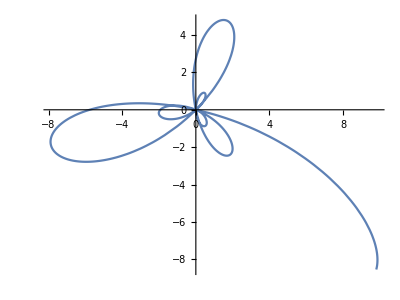

```mathematica
PolarPlot[Fibonacci[n],{n,-7,0}]
```

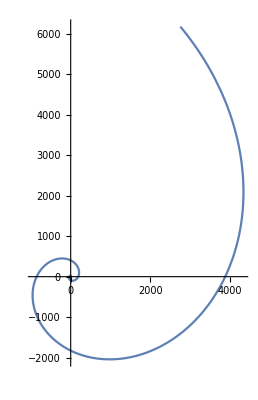

```mathematica
PolarPlot[Fibonacci[n],{n,0,20}]
```

```mathematica
CommunityGraphPlot[Graph[Flatten[Select[{"apology"->"statement","convenience"->"comfort",praise->"glory","praise"->"honor","praise"->"criticism","praise"->"blessing","praise"->"appreciation"},UnsameQ[#,{}]&]]],VertexLabels->"Name"]
```

-Graphics-

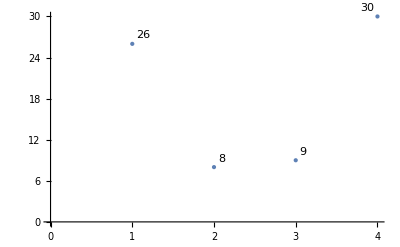

```mathematica
ListPlot[Labeled[#,#]&/@Table[{26,8,9,30}[[n]],{n,4}],PlotStyle->PointSize[Medium]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 1 of Symbol[] does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Part::partw: Part 2 of Symbol[] does not exist.

Part::partw: Part 3 of Symbol[] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

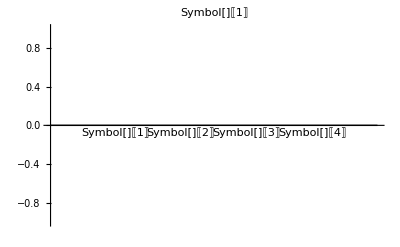
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[BarChart[Labeled[#,#]&/@Table[patientsPerMonth[[All,index]][[All,2]][[n]],{n,4}],PlotLabel->patientsPerMonth[[All,index]][[All,1]][[1]]],{index,1,12}]
```